```mathematica
h=73/10; r2=73/10; r1=2;
```

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{r2,h}],Disk[{0,0},2]];
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
Ωmesh=ToElementMesh[Ω,MaxCellMeasure->.001]
```

ElementMesh[{{0.,7.3},{0.,7.3}},{TriangleElement[<79197>]}]

```mathematica
Ωmesh["Wireframe"]
```

-Graphics-

```mathematica
lpc=D[ϕ[r,z],z,z]+D[ϕ[r,z],r,r]+1/r D[ϕ[r,z],r]; TraditionalForm[lpc]
```

ϕ^(0,2)(r,z)+(ϕ^(1,0)(r,z))/r+ϕ^(2,0)(r,z)

```mathematica
solc=NDSolveValue[
{lpc==NeumannValue[0,r==0&&r1<z<h]+NeumannValue[0,z==0&&r1<r<r2],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==r1^2],
ϕ[r,h]==0,ϕ[r2,z]==0},ϕ,{r,z}∈Ωmesh
]
```

InterpolatingFunction[{{0., 7.3}, {0., 7.3}}, <>]

```mathematica
phiList=Table[Which[r^2+z^2<=r1^2,-1,r>=r2||z>=h,0,True,solc[r,z]],{r,0,730/100,1/100},{z,0,730/100,1/100}];
```

```mathematica
expFormat[x_]:=Module[{exp,neg},
If[StringLength[x]==0,exp="0",exp=x];
neg=StringTake[exp,1]=="-";
If[neg,exp=StringDrop[exp,1]];
If[StringLength[exp]<2,exp="0"<>exp];
If[neg,"-"<>exp,"+"<>exp]
];
eFormat[x_,m_,n_]:=StringPadLeft[If[x==0,StringPadRight["0.",n+1,"0"]<>"E+00",
NumberForm[SetPrecision[x,n],ScientificNotationThreshold->{0,0},NumberFormat->(Row[{#1, "E", expFormat[#3]}] & )]//ToString],m," "];
```

```mathematica
SetDirectory["c:\\git\\ElectronMonteCarlo\\test"]
```

c:\git\ElectronMonteCarlo\test

```mathematica
With[{file=OpenWrite["cwPhi.txt"]},
WriteLine[file,"1/28/2023 Phi from 2D cylindrical solve"];
WriteLine[file,"type cylindrical"];
WriteLine[file,"731 731 .0001 200"];
Do[
WriteLine[file,Row[eFormat[#,12,5]&/@d]],
{d,phiList}
];
Close@file
]
```

cwPhi.txt

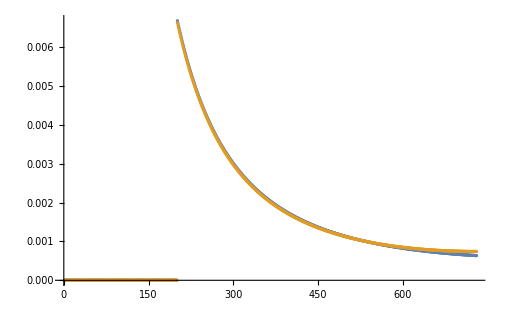

```mathematica
ListPlot[{Differences[phiList[[;;,1]]],Differences[phiList[[1,;;]]]}]
```

```mathematica
a=1/100; (* The lattice spacing *)
```

```mathematica
nearPoints=Select[Flatten[Table[a{i+1/2,j+1/2},{i,0,729},{j,0,729}],1],(2<Sqrt[(#[[1]])^2+(#[[2]])^2]<2.5)&];
```

```mathematica
Length[nearPoints]
```

17672

```mathematica
eFieldFromFile[r_,z_,a_,phi_]:=Module[{i,j,alpha,beta,theta,Er,Ez},
i=Floor[r/a]+1; alpha=r/a-i+1;
j=Floor[z/a]+1; beta=z/a-j+1;
Print["i ",i," alpha ",alpha];
Print["j ",j," beta  ",beta];
Er =1/a((1-alpha)(phi[[i+1,j]]-phi[[i,j]])+alpha(phi[[i+1,j+1]]-phi[[i,j+1]]));
Ez =1/a((1-beta)(phi[[i,j+1]]-phi[[i,j]])+beta(phi[[i+1,j+1]]-phi[[i+1,j]]));
{Er,Ez}
]
```

```mathematica
eFieldFromFile[1.999,.001,a,phiList]
```

i 200 alpha 0.9

j 1 beta  0.1

{0.00151015,0.000167795}

```mathematica
phiList[[200;;201,1;;2]]
```

{{-1,-1},{-1,-0.999983}}

```mathematica
Dimensions[phiList]
```

{731,731}